```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
data1=ToExpression/@StringSplit[#," "]&/@Import["debug_data1.txt","Lines"];
data2=ToExpression/@StringSplit[#," "]&/@Import["debug_data2.txt","Lines"];
maxtime=Max[Max[data1⟦All,1⟧],Max[data2⟦All,1⟧]];
datafr=N[{(#⟦2,1⟧+#⟦1,1⟧)/2,Abs[#⟦2,2⟧-#⟦1,2⟧]}&/@Partition[data1,2],10];
```

```mathematica
maxfilter=Compile[{{l,_Real,2},{r,_Integer}},
{Mean[#⟦All,1⟧],Max[#⟦All,2⟧]}&/@Partition[l,2r+1]
];
meanfilter=Compile[{{l,_Real,2},{r,_Integer}},
{Mean[#⟦All,1⟧],Mean[#⟦All,2⟧]}&/@Partition[l,2r+1]
];
```

```mathematica
fin1=Interpolation[DeleteDuplicates[data1,First[#1]==First[#2]&]];
fin2=Interpolation[DeleteDuplicates[data2,First[#1]==First[#2]&]];
```

```mathematica
Plot[{
fin1[x]
},{x,0,maxtime}]
Plot[{
fin2[x]
},{x,0,maxtime}]
```

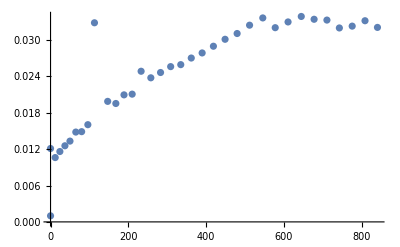

-Graphics-

```mathematica
ListPlot[{data1}]
ListPlot[{data2}]
```

```mathematica
maxfilter[data1,10]
```

maxfilter[{{0,0.001},{0,0.0121066},{12,0.0106117},{24,0.0116077},{37,0.0125574},{50,0.0133268},{65,0.0148185},{80,0.0148856},{96,0.016037},{113,0.0328462},{147,0.0198822},{168,0.0195309},{189,0.0209555},{210,0.0210735},{233,0.0248504},{258,0.0237684},{283,0.0246435},{309,0.0256146},{335,0.0259411},{362,0.0270313},{390,0.0278713},{419,0.0289778},{449,0.0301241},{480,0.0310758},{512,0.0324495},{546,0.0336476},{578,0.0320374},{611,0.0329836},{645,0.0338891},{678,0.0334253},{711,0.0332935},{743,0.0319924},{776,0.032294},{809,0.0331833},{841,0.0320832}},10]

```mathematica
ListLogPlot[{
{#⟦1⟧,1000#⟦2⟧}&/@maxfilter[data1,2],
maxfilter[data2,2]
}]
```

```mathematica
ListLogPlot[{
{#⟦1⟧,1000#⟦2⟧}&/@maxfilter[data1,2],
meanfilter[data2,2]
}]
```